```mathematica
(** НАБОР ДАННЫХ ЯВЛЯЕТСЯ МОДЕЛЬНЫМ **)
SetDirectory@NotebookDirectory[];
{DataColumns={"ChipTest1","ChipTest2"},Data=RandomSample[#,118]}&@Import["microchip.csv","Data"];
Dimensions@#&/@%
{Data,DataLabels}={Data⟦All,;;2⟧,Data⟦All,3⟧};
```

{{2},{118,3}}

```mathematica
ClearAll[pass,fail]
pass=Flatten@Position[DataLabels,1];
fail=Complement[Range[118],pass];
```

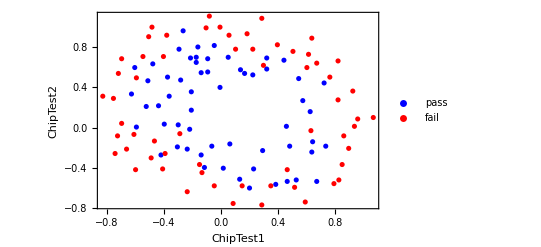

```mathematica
Fig0=ListPlot[{Data⟦pass⟧,Data⟦fail⟧},PlotLegends->{"pass","fail"},PlotStyle->{{Blue,Large},{Red,Large}},Frame->True,FrameLabel->DataColumns]
```

```mathematica
Select[Flatten[Table[{d1,d2},{d1,0,3},{d2,0,3}],1],Plus@@#≤3&]
```

{{0,0},{0,1},{0,2},{0,3},{1,0},{1,1},{1,2},{2,0},{2,1},{3,0}}

```mathematica
ClearAll[kmExtendDim];
kmExtendDim=Function[{d,x,y},Map[Times@@({x,y}^#)&,#]&@Select[Flatten[Table[{d1,d2},{d1,0,d},{d2,0,d}],1],Plus@@#≤d&]]
```

Function[{d,x,y},((Times@@{x,y}^#1&)/@#1&)[Select[Flatten[Table[{d1,d2},{d1,0,d},{d2,0,d}],1],Plus@@#1≤d&]]]

```mathematica
ClearAll[kmExtendData];
kmExtendData[Data_,d_Integer?Positive]:=Map[kmExtendDim[d,Sequence@@#]&,Data]
```

```mathematica
kmExtendDim[5,x1,x2]
```

{1,x2,x2^2,x2^3,x2^4,x2^5,x1,x1 x2,x1 x2^2,x1 x2^3,x1 x2^4,x1^2,x1^2 x2,x1^2 x2^2,x1^2 x2^3,x1^3,x1^3 x2,x1^3 x2^2,x1^4,x1^4 x2,x1^5}

```mathematica
Dimensions[Features=kmExtendData[Data,5]]
```

{118,21}

```mathematica
ClearAll[Sigma];
Sigma=Function[Z,1/(1+Exp[-Z])];
```

```mathematica
ClearAll[LinearLeastSquares];
(** 
Решение задачи M.a=b
M - матрица выборки (m×[n+1])
b - вектор-столбец ответов (m×1)
a - вектор-столбец искомых параметров ([n+1]×1)	
**)
LinearLeastSquares[M_,b_]:=Inverse[Transpose[M].M].(b.M)
```

```mathematica
ClearAll[LogisticFitInit,LogisticFitStep,LogisticFit];
LogisticFitInit[Features_,Answers_,n_,reg_]:=(
b=Prepend[ConstantArray[0,n],N@Log[#/(1-#)]&[Mean[Answers]]];
τ=reg;
);
LogisticFitStep[Features_,Answers_]:=Block[{Z,p,w,W,U,n},
n=Length@Features⟦1⟧;
Z=Features.b;
p=Sigma[Z];
w=p*(1-p);
W=DiagonalMatrix[w];
U=Z+(Answers-p)/w;
LinearLeastSquares[Transpose[Features].W.Features+τ IdentityMatrix[n],Transpose[Features].W.U]
]
LogisticFit[Features_,Answers_,reg_,iterations_]:=Block[{n,b,bNew,i,τ},
n=Length@Features⟦1⟧-1;
LogisticFitInit[Features,Answers,n,reg];
For[i=1,i≤iterations,i++,
bNew=LogisticFitStep[Features,Answers];
b=bNew;
];
Return@b;
]
```

```mathematica
LogisticFitInit[Features,DataLabels,20,.5]
```

```mathematica
LogisticFitStep[Features,DataLabels]
```

{1.42718,1.41131,-1.99684,-0.213855,-1.50812,-0.272301,0.774558,-1.2983,-0.31874,-0.215819,-0.189016,-2.49399,-0.418748,-0.825064,-0.354892,0.24924,0.130877,0.0220368,-1.81058,-0.166545,-0.121251}

```mathematica
ClearAll[τ1,τ2];
τ1=0.05;
τ2=0.001;
τ3=10;
```

```mathematica
weights1=LogisticFit[Features,DataLabels,τ1,20]
```

{3.18936,3.54902,-5.1802,-1.00286,-3.7236,0.146289,2.12166,-4.32584,-0.154303,-1.78255,-1.93385,-5.05319,-1.19428,-2.29122,-1.68243,0.851427,1.55226,1.42449,-4.89486,-0.463992,-1.39067}

```mathematica
weights2=LogisticFit[Features,DataLabels,τ2,20]
```

{3.64488,5.17307,-1.77608,-6.02982,-16.4883,11.8998,0.843587,-9.52285,9.34319,-0.845011,-17.4639,-3.85239,6.10421,-13.6529,-10.2899,6.68274,5.09196,13.4848,-9.8855,-5.85814,-7.58853}

```mathematica
weights3=LogisticFit[Features,DataLabels,τ3,20]
```

{0.197974,0.160292,-0.254988,-0.121022,-0.296142,-0.210237,-0.0179093,-0.115276,-0.0615297,-0.0283706,-0.0395806,-0.416899,-0.0571754,-0.111574,-0.0490681,-0.0788361,-0.0144886,-0.0214717,-0.333063,-0.037196,-0.124794}

```mathematica
LogisticRegFit=LogitModelFit[{Features,DataLabels}];
```

```mathematica
ClearAll[kmContourLine];
kmContourLine[W_,dim_,opts___]:=ContourPlot[Plus@@(W*kmExtendDim[dim,x,y])==0,{x,-1,1},{y,-1,1},opts]
```

```mathematica
Fig1=kmContourLine[LogisticRegFit⟦1,2⟧,5,ContourStyle->Black,PlotLegends->{"τ-Wolfram"}];
Fig2=kmContourLine[weights1,5,ContourStyle->Green,PlotLegends->{"τ1="<>ToString[τ1]}];
Fig3=kmContourLine[weights2,5,ContourStyle->Orange,PlotLegends->{"τ2="<>ToString[τ2]}];
Fig4=kmContourLine[weights3,5,ContourStyle->Cyan,PlotLegends->{"τ3="<>ToString[τ3]}];
```

Регуляризация помогает контролировать качество обучения модели. Так,например, если параметр регуляризации выбрать слишком большим, то задача, решаемая с помощью МНК будет аппроксимировать шумы и модель обучится неправильно. Если параметр регуляризации положить меньше некторого оптимального значения, то наоборот, модель недостаточно обучится. На диаграмме выше можно заметить, что оптимальное значение параметра регуляризации находится около τ2.

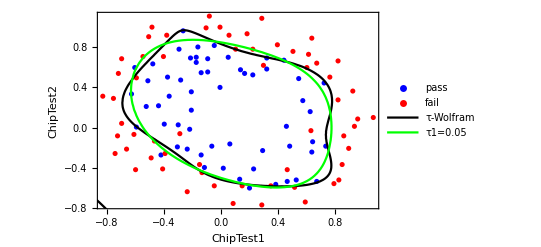

```mathematica
Show[Fig0,Fig1,Fig2]
```

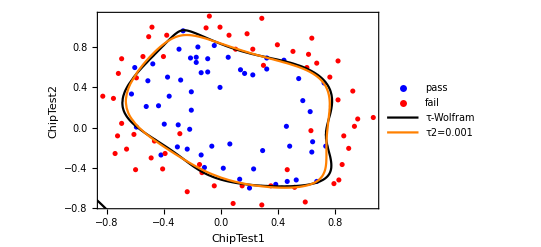

```mathematica
Show[Fig0,Fig1,Fig3]
```

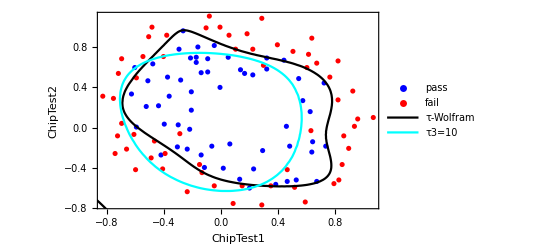

```mathematica
Show[Fig0,Fig1,Fig4]
```